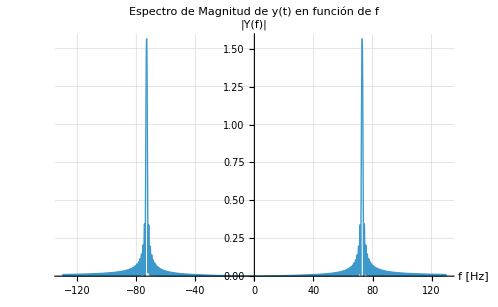

```mathematica
Y[w_]:=(Pi/I)*((Sin[(w-2*Pi*f0)*T]/(w-2*Pi*f0))+(Sin[(w+2*Pi*f0)*T]/(w+2*Pi*f0)));

(*Parámetros*)
f0=73;       (*frecuencia central en Hz*)
T=0.5;       (*duración de la ventana[s]*)

(*Gráfico con eje en frecuencia lineal[Hz]*)
Plot[Abs[Y[2*Pi*f]],(*evaluamos Y en w=2πf*){f,-130,130},(*rango del eje en Hz*)PlotRange->All,AxesLabel->{"f [Hz]","|Y(f)|"},PlotLabel->"Espectro de Magnitud de y(t) en función de f",PlotPoints->100,PlotStyle->Thick,GridLines->Automatic]
```

```mathematica
Export["C:\\Users\\bruno\\OneDrive\\Desktop\\ok.svg",%83,"SVG"]
```

C:\Users\bruno\OneDrive\Desktop\ok.svg

```mathematica
Plot[Abs[Y[2 π f]],{f,-130,130},Filling->Automatic,PlotRange->All,AxesLabel->{"f [Hz]","|Y(f)|"},PlotLabel->"Espectro de Magnitud de y(t) en función de f",PlotPoints->100,PlotStyle->Thick,GridLines->Automatic]
```